```mathematica
Puas := fi''[x] == a/(√(fi[x] - b x^2));
```

```mathematica
a =1;
b=0.1;
```

```mathematica
NDSolve[{y''[x]+ 1/x y'[x] == a^2/(√y[x]), y[0.001]==0.001, y'[0.001]== 0.001},y[x], {x, 0.001, 0.013}]
```

{{y[x]→InterpolatingFunction[{{0.001, 0.013}}, <>][x]}}

```mathematica
f[fi_,x_] := a^2/(√(fi - b^2 x^2))
```

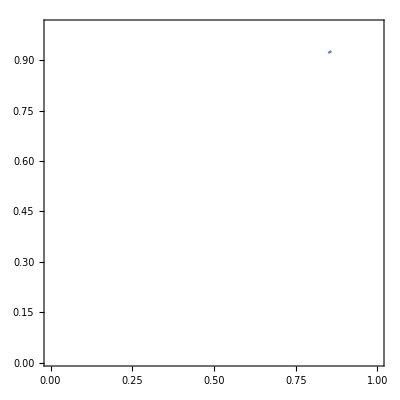

```mathematica
ContourPlot[f[fi, x]==0, {fi, 0, 1}, {x, 0.01, 1}]
```

```mathematica
a =1;
b=√(1.4400000000000003*^8);
```

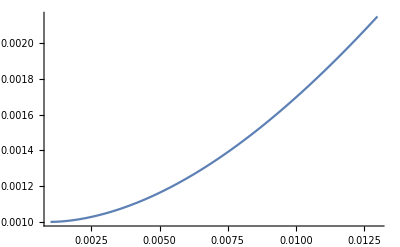

```mathematica
s =NDSolve[{y''[x]+ 1/x y'[x] == a^2/(√y[x]), y[0.001]==0.001, y'[0.001]== 0.001},y[x], {x, 0.001, 0.013}];
Plot[Evaluate[y[x]/.s], {x, 0.001,0.013}]
```

```mathematica
Integrate[1/x(f^2)[x],x]
```

∫(f^2[x])/x ⅆx